# Oscillations

## Juan Jose Neri

### Problem 5.39

-Graphics-

The equation (5.48) is: x^(..)+2β ẋ+ω_0^2 x=f(t)

Here ω_0=5 ω and ω=2π from which ω_0=10π

β=ω_0/20=π/2

f=f_0 cos(ω t)=1000 cos(2π t)

∴ Equation (1) becomes:

x^(..)+π ẋ+100 π^2 x=1000 cos(2π t)

```mathematica
NDSolve[{
x''[t]+π*x'[t]+100 π^2 *x[t]==1000 Cos[2π t],
x[0]==0,
x'[0]==0
},x,{t,0,4}]
```

{{x→InterpolatingFunction[{{0., 4.}}, <>]}}

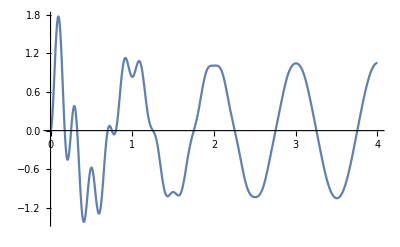

```mathematica
Plot[Evaluate[x[t]/.%],{t,0,4}]
```

Which agrees with figure (5.15)